```mathematica
On[Assert];
Import[NotebookDirectory[]<>"/DensityMatrixTools.wl"]
```

### Tests

#### Initialize a 3 q-bit density matrix

```mathematica
ThermalQBit[a,Q1]
```

DM[<|data→SparseArray[…],qbitIDs→<|Q1→1|>,nqbit→1|>]

```mathematica
ρ1= NThermalQBit[{a1,a2}]
```

DM[<|data→SparseArray[…],qbitIDs→<|𝒬_1→1,𝒬_2→2|>,nqbit→2|>]

#### Test Multiplication

```mathematica
ρ1⊗NThermalQBit[{a2,a3,a4},{Subscript[𝒬, 3],Subscript[𝒬, 4],Subscript[𝒬, 5]}]
```

DM[<|data→SparseArray[…],qbitIDs→<|𝒬_1→1,𝒬_2→2,𝒬_3→3,𝒬_4→4,𝒬_5→5|>,nqbit→5|>]

```mathematica
NThermalQBit[{a2,a3,a4},{Subscript[𝒬, 3],Subscript[𝒬, 4],Subscript[𝒬, 5]}]⊗ρ1
```

DM[<|data→SparseArray[…],qbitIDs→<|𝒬_3→1,𝒬_4→2,𝒬_5→3,𝒬_1→4,𝒬_2→5|>,nqbit→5|>]

#### Test ReOrder

ReOrdering to the same order shouldn’t change a DM.

```mathematica
Assert[ReOrder[ρ1,<| Subscript[𝒬, 1]-> 1,Subscript[𝒬, 2]-> 2|>]==ρ1]
```

ReOrdering to any order and back to the same order should Leave the density matrix unchanged

```mathematica
Assert[ReOrder[ReOrder[ρ1,<| Subscript[𝒬, 1]-> 2,Subscript[𝒬, 2]-> 1|>],<| Subscript[𝒬, 1]-> 1,Subscript[𝒬, 2]-> 2|>]==ρ1]
```

Generating a new density matrix in a different order and reordering should give the same density matrix

```mathematica
Assert[ReOrder[ NThermalQBit[{a2,a1},{Subscript[𝒬, 2],Subscript[𝒬, 1]}],<| Subscript[𝒬, 1]-> 1,Subscript[𝒬, 2]-> 2|>]==ρ1]
```

#### Test Partial Trace

```mathematica
Assert[(PTR[ρ1,{Subscript[𝒬, 1],Subscript[𝒬, 2]}][data]//Simplify//Normal)=={{1}}]
```

```mathematica
Assert[PTR[ NThermalQBit[{a3,a1,a2},{Q3,Q1,Q2}],{Q1,Q2}]===
PTR[ NThermalQBit[{a2,a1,a3},{Q2,Q1,Q3}],{Q1,Q2}]===PTR[ NThermalQBit[{a1,a3,a2},{Q1,Q3,Q2}],{Q1,Q2}]]
```

### Examples

#### Evolving a 4 q-bit system

```mathematica
ρ = NThermalQBit[{p1,p2,p3,p4}];
Hi = SparseArray[{{13,4}->I,{4,13}-> -I},{16,16}];
Ui =MakeDM[ SparseArray[MatrixExp[I Hi θ]]];
```

```mathematica
Ui.ρ.Transpose[Ui]
```

DM[<|data→SparseArray[…],qbitIDs→<|𝒬_1→1,𝒬_2→2,𝒬_3→3,𝒬_4→4|>,nqbit→4|>]

#### Evolving an 8 q-bit system

Initialize a thermal 8 qbit system.

```mathematica
ρ = NThermalQBit[{p1,p2,p3,p4,p5,p6,p7,p8}];
SubsysInteraction = SparseArray[{{13,4}->I,{4,13}-> -I},{16,16}];
Hi1 = KroneckerProduct[SubsysInteraction,IdentityMatrix[2^4]];
Hi2= KroneckerProduct[IdentityMatrix[2^4],SubsysInteraction];
```

First time step.

```mathematica
Ui =MakeDM[ SparseArray[MatrixExp[I (Hi1+Hi2) θ]]];
ρ = Ui.ρ.Transpose[Ui];
```

Second time step

```mathematica
newOrder =
<|Subscript[𝒬, 1]-> 5,Subscript[𝒬, 2]-> 6,Subscript[𝒬, 3]-> 3,Subscript[𝒬, 4]-> 4,Subscript[𝒬, 5]-> 1,Subscript[𝒬, 6]-> 2,Subscript[𝒬, 7]-> 7,Subscript[𝒬, 8]-> 8|>;
Ui =ReOrder[MakeDM[ SparseArray[MatrixExp[I (Hi1+Hi2) θ]],newOrder],ρ[qbitIDs]];
```

```mathematica
ρ = Ui.ρ.Transpose[Ui];
```

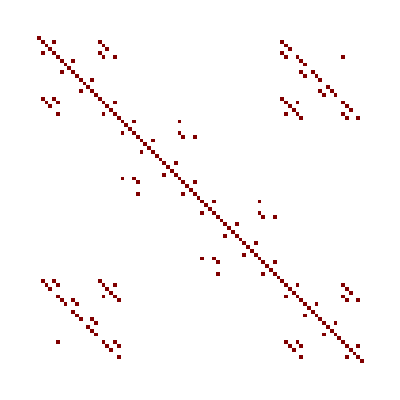

```mathematica
ρ//Show
```

### Generating a Random Hamiltonian

```mathematica
n = 4
```

```mathematica
F[a_,b_]:= a-> b
```

```mathematica
Outer[F,Permutations[{1,0,0,0}],Permutations[{1,0,0,0}],1]//MatrixForm
Permutations[{0,1,1,0}]
Permutations[{1,1,1,0}]

p = Permutations[{1,0,0,0}];
index = FromDigits[#,2]&/@p;
```

```mathematica
index
```

{8,4,2,1}

```mathematica
Flatten[Table[Table[F[index[[i]],index[[j]]],{j,i-1}],{i,Length[Permutations[{1,0,0,0}]]}]]
```

{4→8,2→8,2→4,1→8,1→4,1→2}

```mathematica
FromDigits[{1,0},2]
```

10

```mathematica
ConstantArray[0,{2^4,2^4}][[5,9]]=1
```

Set::setps: ConstantArray[0,{2^4,2^4}] in the part assignment is not a symbol.

1

```mathematica
p
```

{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}

```mathematica
FromDigits[{1,1,1,1},2]
```

15

```mathematica
p = Permutations[Table[]];
```

```mathematica
RandomHamiltonian[3,10]
```

{1,1,1,0,0,0,0,0,0,0}

```mathematica
RandomHamiltonian[Energy_,nqbits_]:=Module[{protoState,perms,indeces},
protoState = Table[If[i<Energy+1,1,0],{i,nqbits}];
perms = Permutations[protoState];
indeces = FromDigits[#,2]&/@perms;
Plus@@Flatten[Table[Table[A[i+1,j+1]MakeHamiltonian[indeces[[i]],indeces[[j]],nqbits],{j,i-1}],{i,Length[perms]}],1]
]
```

```mathematica
MakeHamiltonian[i1_,i2_,n_]:=SparseArray[{{i1,i2}->1,{i2,i1}->1},2^n]
```

```mathematica
s=SparseArray[{{1,1}->1,{2,2}->2,{3,3}->3,{1,3}->4}]
```

```mathematica
Clear[A]
```

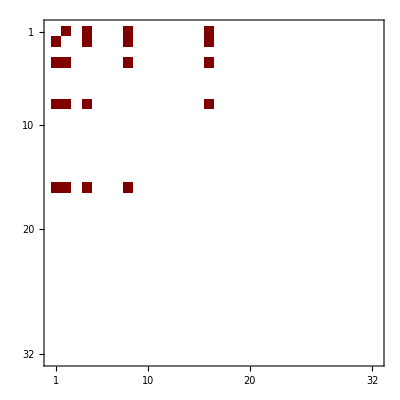

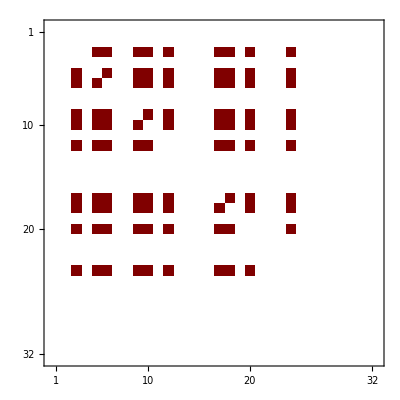

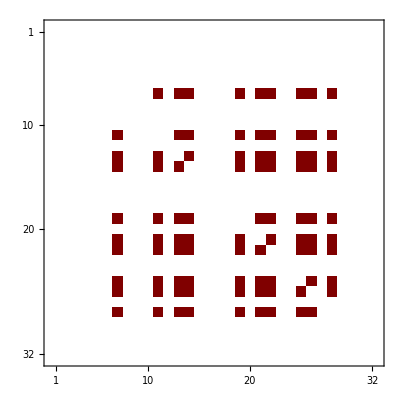

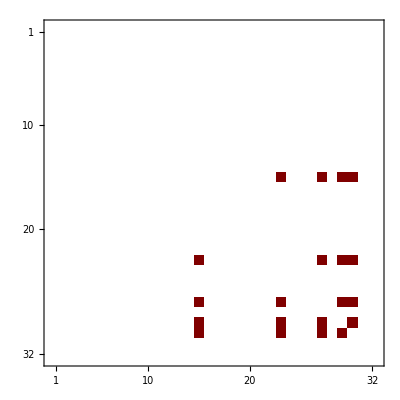

```mathematica
MatrixPlot[RandomHamiltonian[1,5]]
MatrixPlot[RandomHamiltonian[2,5]]
MatrixPlot[RandomHamiltonian[3,5]]
MatrixPlot[RandomHamiltonian[4,5]]
```

```mathematica
RandomHamiltonian[3,11]
```

SparseArray[<27060>, {2048, 2048}]

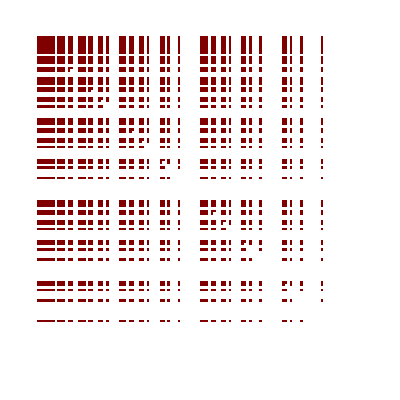

```mathematica
MatrixPlot[%,Frame-> None]
```

```mathematica
Random
```

```mathematica
RandomHamiltonian[3,4]
```

dimensionMismatch::value: 2^nqbits must be equal to the size of the matrix instead of nqbits = 0 and matrixdim = 16

General::stop: Further output of dimensionMismatch::value will be suppressed during this calculation.

Null A[3,2]+Null A[4,2]+Null A[4,3]+Null A[5,2]+Null A[5,3]+Null A[5,4]

## TESTS

```mathematica
RandomHamiltonian[1,2]
```

DM[<|data→SparseArray[…],qbitIDs→<|𝒬_1→1,𝒬_2→2|>,nqbit→2|>]